# Homework 2

## Sohyeon Park, Sam Morabito

### I should not forget to add 6B and 8!!! Problem 1

```mathematica
system1={a'[t]==p-r*a[t],a[0]==0.0001};
```

```mathematica
parameter1={p->0.5,r->0.5};
```

```mathematica
solset1=NDSolve[system1/.parameter1,{a[t]},{t,0,20}];
```

```mathematica
system2={b'[t]==q*b[t]^m/(j^m+b[t]^m)-s*b[t],b[0]==0.0001};
```

```mathematica
parameter2={q->2,j->1,m->1,s->1};
```

```mathematica
solset2=NDSolve[system2/.parameter2,{b[t]},{t,0,20}];
```

```mathematica
system3={c'[t]==u*h^n/(h^n+c[t]^n)-w*c[t],c[0]==0.0001};
```

```mathematica
parameter3={u->2,h->1,n->1,w->1};
```

```mathematica
solset3=NDSolve[system3/.parameter3,{c[t]},{t,0,20}];
```

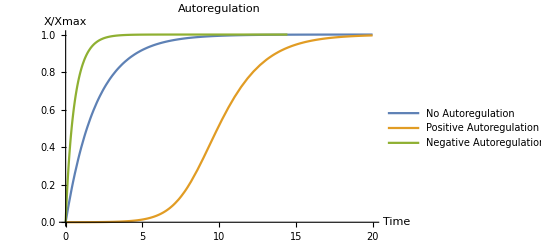

```mathematica
Plot[{{a[t]/.solset1},{b[t]/.solset2},{c[t]/.solset3}},{t,0,20},PlotRange->{0,1},PlotStyle->Thick,AxesLabel->{"Time","X/Xmax"},PlotLabel->"Autoregulation",PlotLegends->Placed[{"No Autoregulation","Positive Autoregulation","Negative Autoregulation"},Right]]
```

#### Problem 2A Positive sequential activation cascades x->y->z

```mathematica
system4={
x'[t]==1-x[t],
y'[t]==q*x[t]^m/(j^m+x[t]^m)-r*y[t],
z'[t]==p*y[t]^n/(i^n+y[t]^n)-s*z[t]
};
```

```mathematica
parameter4={q->2,j->1,m->3,p->2,i->1,n->3,r->1,s->1};
```

```mathematica
initial4={x[0]==.0001,y[0]==.0001,z[0]==.0001};
```

```mathematica
newsystem4=Join[system4,initial4];
```

```mathematica
solveset4=NDSolve[newsystem4/.parameter4,{x[t],y[t],z[t]},{t,0,8}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}}

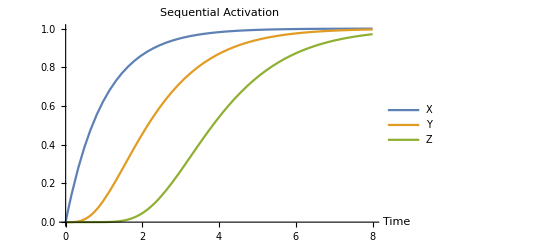

```mathematica
Plot[{x[t]/.solveset4,y[t]/.solveset4,z[t]/.solveset4},{t,0,8},PlotRange->{{0,8},{0,1}},PlotStyle->Thick,AxesLabel->{"Time"},PlotLabel->"Sequential Activation",PlotLegends->Placed[{"X","Y","Z"},Right]]
```

### Problem 2B

#### Hill number = 1

```mathematica
system5={
x'[t]==1-x[t],
y'[t]==q*x[t]^m/(j^m+x[t]^m)-r*y[t],
z'[t]==p*y[t]^n/(i^n+y[t]^n)-s*z[t]
};
```

```mathematica
parameter5={q->2,j->1,m->1,p->2,i->1,n->1,r->1,s->1};
```

```mathematica
initial5={x[0]==.0001,y[0]==.0001,z[0]==.0001};
```

```mathematica
newsystem5=Join[system5,initial5];
```

```mathematica
solveset5=NDSolve[newsystem5/.parameter5,{x[t],y[t],z[t]},{t,0,6}];
```

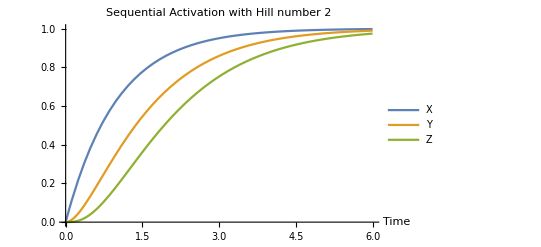

```mathematica
Plot[{x[t]/.solveset5,y[t]/.solveset5,z[t]/.solveset5},{t,0,6},PlotRange->{{0,6},{0,1}},PlotStyle->Thick,AxesLabel->{"Time"},PlotLabel->"Sequential Activation with Hill number 2",PlotLegends->Placed[{"X","Y","Z"},Right]]
```

Compared to problem 2A which uses hill number>1, here I can observe sequential activation happens pretty fast (not much delay)

### Problem 3

```mathematica
pulseStart = 1; pulseStop = 6;
pulse[time_,pulseAmplitude_]:=Piecewise[{{0, time<pulseStart},{pulseAmplitude, pulseStop≥time≥pulseStart},{0,time>pulseStop}}];
```

```mathematica
system6 = {
x'[t]==pulse[t, xmax]-d x[t],
y'[t]==pmax1* x[t]^m/(j^m+x[t]^m)-r y[t],
z'[t]== pmax2* x[t]^n/(h^n+x[t]^n)-s z[t],
z[0]==0.001,
y[0]==0.001,
x[0]==0.001};
```

```mathematica
d=1;TFss=1; (* it's convenient to set these globally *)
parameter6 = {pmax1->2,pmax2->2,r->1,j->1, xmax->TFss*d,h->2,s->.6,n->1,m->1};
```

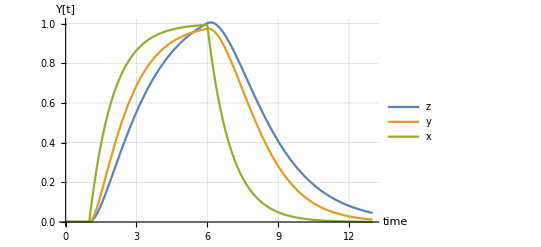

```mathematica
ExactSolution6=NDSolve[system6/.parameter6,{x[t],y[t],z[t]},{ t,0,13}];
Plot[
{z[t]/.ExactSolution6,
y[t]/.ExactSolution6,
x[t]/.ExactSolution6},
{t,0,13}, PlotRange->Automatic,PlotStyle->Thick,GridLines->Automatic,AxesLabel-> {"time"," Y[t]"},PlotLegends->{"z","y","x"}]
```

```mathematica
(* we want to see activation roughly one minute apart for x,y,z *)
Manipulate[
parameter6 = {pmax1->pmax1val,pmax2->pmax2val,r->rval,j->jval, xmax->TFss*d,h->hval,s->sval,n->nval,m->mval};
ExactSolution6=NDSolve[system6/.parameter6,{x[t],y[t],z[t]},{ t,0,13}];
Plot[
{z[t]/.ExactSolution6,
y[t]/.ExactSolution6,
x[t]/.ExactSolution6},
{t,0,13}, PlotRange->{0,1},PlotStyle->Thick,GridLines->Automatic,AxesLabel-> {"time"," Y[t]"},PlotLegends->{"z","y","x"}],
{{pmax1val,1},0,10, Appearance-> "Labeled"},
{{pmax2val,1},0,10, Appearance-> "Labeled"},
{{rval,1},0,10, Appearance-> "Labeled"},
{{jval,1},0,10, Appearance-> "Labeled"},
{{hval,1},0,10, Appearance-> "Labeled"},
{{sval,1},0,10, Appearance-> "Labeled"},
{{nval,1},0,20, Appearance-> "Labeled"},
{{mval,1},0,10, Appearance-> "Labeled"}]
```

### Problem 4

```mathematica
pulseStart1 = 3; pulseStop1 = 4; pulseStart2=10; pulseStop2=15;
pulse1[time_,pulseAmplitude_]:=Piecewise[{{0, time<pulseStart1},{pulseAmplitude, pulseStop1≥time≥pulseStart1},{0,pulseStart2>time>pulseStop1},{pulseAmplitude, pulseStop2≥time≥pulseStart2},{0,time>pulseStop2}}];
```

```mathematica
parametersys={j->1,r->1,h->1,s->1,m->1,n->1};
```

```mathematica
sys={
x[t]==pulse1[t, 1],
y'[t]==2*x[t]^m/(j^m+x[t]^m)-r y[t],
z'[t]==4*y[t]^n/(h^m+y[t]^n)*x[t]^m/(j^m+x[t]^m)-s z[t],
y[0]==0.01,z[0]==0.01}
```

{x[t]==(Piecewise[{{0, t<3}, {1, 4≥t≥3}, {0, 10>t>4}, {1, 15≥t≥10}, {0, True}}]),y'[t]==(2 x[t]^m)/(j^m+x[t]^m)-r y[t],z'[t]==(4 x[t]^m y[t]^n)/((j^m+x[t]^m) (h^m+y[t]^n))-s z[t],y[0]==0.01,z[0]==0.01}

```mathematica
solution6=NDSolve[sys/.parametersys,{x[t],y[t],z[t]}, {t,0,20}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}}

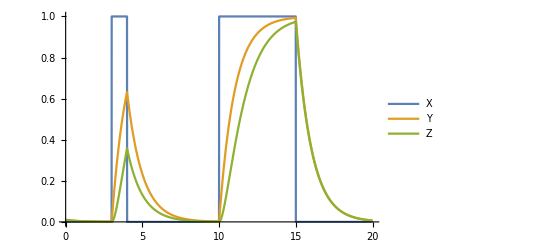

```mathematica
Plot[{x[t]/.solution6,y[t]/.solution6,z[t]/.solution6},{t,0,20},PlotLegends->{"X","Y","Z"}]
```

### Problem 5A

```mathematica
system7={
x'[t]==0,
y'[t]==2*x[t]^n/(j^n+x[t]^n)-r y[t],
z'[t]==pmax*h^m/(h^m+y[t]^m)*x[t]^p/(j^p+x[t]^p)-s z[t],
x[0]==1,y[0]==0,z[0]==0
};
```

```mathematica
parameter7={pmax->4,j->1,r->1,h->1,s->1,m->2,n->2,p-> 3};
```

```mathematica
numericsol7=NDSolve[system7/.parameter7,{x[t],y[t],z[t]},{t,0,10}];
```

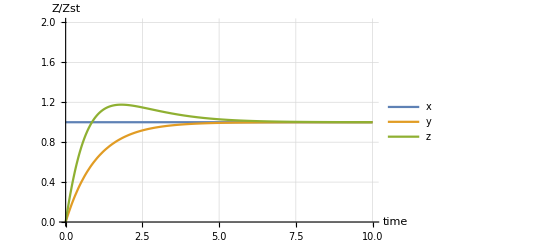

```mathematica
Plot[{x[t]/.numericsol7,y[t]/.numericsol7,z[t]/.numericsol7},{t,0,10}, PlotRange->{0,2},PlotStyle->Thick,GridLines->Automatic,AxesLabel-> {"time"," Z/Zst"},PlotLegends->{"x","y","z"}]
```

### Problem 5B

```mathematica
system7={
x'[t]==0,
 y'[t]==2/1000*x[t]^n/(j^n+x[t]^n)-r /1000 y[t],
z'[t]==pmax*h^m/(h^m+y[t]^m)*x[t]^p/(j^p+x[t]^p)-s z[t],
x[0]==1,y[0]==0,z[0]==0
};
```

```mathematica
parameter7={pmax->4,j->1,r->1,h->1,s->1,m->2,n->2,p-> 3};
```

```mathematica
numericsol7=NDSolve[system7/.parameter7,{x[t],y[t],z[t]},{t,0,10000}];
```

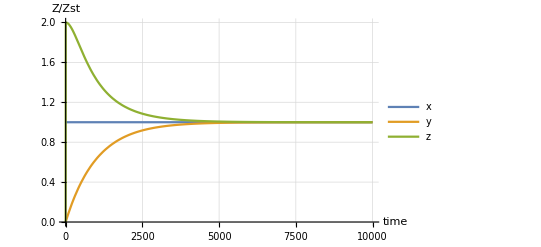

```mathematica
Plot[{x[t]/.numericsol7,y[t]/.numericsol7,z[t]/.numericsol7},{t,0,10000}, PlotRange->{0,2},PlotStyle->Thick,GridLines->Automatic,AxesLabel-> {"time"," Z/Zst"},PlotLegends->{"x","y","z"}]
```

Here Z value jumps dramatically within short period of time, so this is more pulse-like. I induced this by increasing hill number since by doing that I can make system more sensitive.

## Problem 6A *Both joint on

```mathematica
system8={
x'[t]==pmax1*y[t]^m/(j^m+y[t]^m)-r x[t],
y'[t]==pmax2*x[t]^n/(h^n+x[t]^n)-s y[t],

x[0]==7,y[0]==0};
```

```mathematica
parameter={pmax1->2,j->1,m->2,r->1,pmax2->2,n->2,h->1,s->1};
```

```mathematica
solsystem8=NDSolve[system8/.parameter,{x[t],y[t]},{t,0,40}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

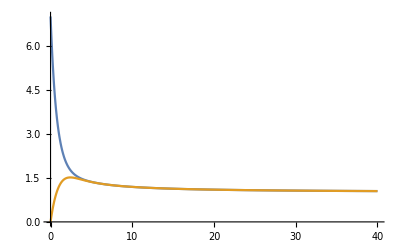

```mathematica
Plot[{x[t]/.solsystem8,y[t]/.solsystem8},{t,0,40},PlotRange->All]
```

both joint off

```mathematica
system8={
x'[t]==pmax1*y[t]^m/(j^m+y[t]^m)-r x[t],
y'[t]==pmax2*x[t]^n/(h^n+x[t]^n)-s y[t],

x[0]==.7,y[0]==0};
```

```mathematica
parameter={pmax1->2,j->1,m->2,r->1,pmax2->2,n->2,h->1,s->1};
```

```mathematica
solsystem8=NDSolve[system8/.parameter,{x[t],y[t]},{t,0,40}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

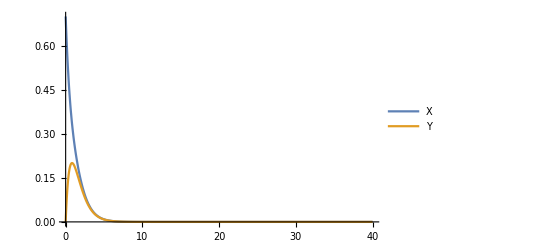

```mathematica
Plot[{x[t]/.solsystem8,y[t]/.solsystem8},{t,0,40},PlotRange->All,PlotLegends->{"X","Y"}]
```

### Problem 6B

### Problem 7(Part 1)

```mathematica
pulseStart = 2; pulseStop = 4;
pulse2[time_,pulseAmplitude_]:=Piecewise[{{0.05, time<pulseStart},{pulseAmplitude, pulseStop≥time≥pulseStart},{0.05,time>pulseStop}}];
```

```mathematica
system9={
5 * x'[t]==x[t]^m/(j^m+x[t]^m)+z[t]^n/(h^n+z[t]^n)+y[t]^l/(i^l+y[t]^l)-1*x[t],
5* y'[t]==x[t]^q/(k^q+x[t]^q)+z[t]^u/(b^u+z[t]^u)+y[t]^v/(c^v+y[t]^v)- 1*y[t],
z[t]==pulse2[t, 1],

x[0]==0.0001,y[0]==0.0001};
```

```mathematica
parameterval={j->2,h->1.9,i->0.5,k->0.5,b->1,c->2,m->1,n->1,l->1,q->1,u->1,v->1,xmax->1};
```

```mathematica
solset=NDSolve[system9/.parameterval,{x[t],y[t],z[t]},{t,0,20}];
```

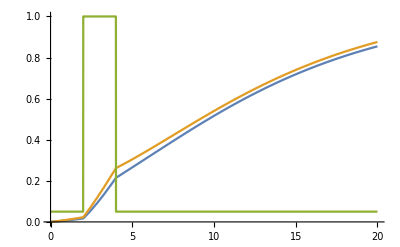

```mathematica
Plot[{x[t]/.solset,y[t]/.solset,z[t]/.solset},{t,0,20},PlotRange->All]
```

```mathematica
Manipulate[parameterval={j->jval,h->hval,i-> ival,k->kval,b->bval,c->cval,m->mval,n->nval,l->lval,q->qval,u->uval,v->vval,xmax->xmaxval};
solset=NDSolve[system9/.parameterval,{x[t],y[t],z[t]},{t,0,50}];
Plot[{x[t]/.solset,y[t]/.solset,z[t]/.solset},{t,0,50},PlotRange->All],
{{jval, 2}, 0.1,10, Appearance->"Labeled"},
{{hval, 1.9}, 0.1,10, Appearance->"Labeled"},
{{ival, 0.5}, 0.1,10, Appearance->"Labeled"},
{{kval, 0.5}, 0.1,10, Appearance->"Labeled"},
{{bval, 1}, 0.1,10, Appearance->"Labeled"},
{{cval, 2}, 0.1,10, Appearance->"Labeled"},
{{mval, 1}, 0.1,10, Appearance->"Labeled"},
{{nval, 1}, 0.1,10, Appearance->"Labeled"},
{{lval, 1}, 0.1,10, Appearance->"Labeled"},
{{qval, 1}, 0.1,10, Appearance->"Labeled"},
{{uval, 1}, 0.1,10, Appearance->"Labeled"},
{{vval, 1}, 0.1,10, Appearance->"Labeled"},
{{xmaxval, 1}, 0.1,10, Appearance->"Labeled"}]
```

#### Problem 7(Part 2) scenario 1.

We can safely delete the arrow coming out from Z to Y since even though we do this, this will not change dynamics since Z essentially activates Y through X.

```mathematica
pulseStart = 2; pulseStop = 4;
pulse2[time_,pulseAmplitude_]:=Piecewise[{{0.05, time<pulseStart},{pulseAmplitude, pulseStop≥time≥pulseStart},{0.05,time>pulseStop}}];
```

```mathematica
system9={
5 * x'[t]==x[t]^m/(j^m+x[t]^m)+z[t]^n/(h^n+z[t]^n)+y[t]^l/(i^l+y[t]^l)-1*x[t],
5* y'[t]==x[t]^q/(k^q+x[t]^q)+y[t]^v/(c^v+y[t]^v)- 1*y[t],
z[t]==pulse2[t, 1],

x[0]==0.0001,y[0]==0.0001};
```

```mathematica
parameterval={j->2,h->1.9,i->0.5,k->0.5,b->1,c->2,m->1,n->1,l->1,q->1,u->1,v->1,xmax->1};
```

```mathematica
solset=NDSolve[system9/.parameterval,{x[t],y[t],z[t]},{t,0,20}];
```

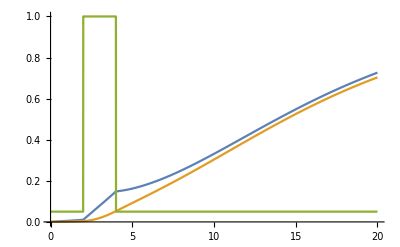

```mathematica
Plot[{x[t]/.solset,y[t]/.solset,z[t]/.solset},{t,0,20},PlotRange->All]
```